# Метод обратной параболической интерполяции

Выполнил:Cайков Константин 
 Группа:ПМ1801

```mathematica
parabolINTER[xn2_,xn1_,xn_,f]:=(f[xn1]*f[xn]*xn2)/((f[xn2]-f[xn1])*(f[xn2]-f[xn]))+ (f[xn2]*f[xn]*xn1)/((f[xn1]-f[xn2])*(f[xn1]-f[xn]))+(f[xn2]*f[xn1]*xn)/((f[xn]-f[xn2])*(f[xn]-f[xn1]))
```

```mathematica
f[x_]:=x^3+6 x^2+6x+1
```

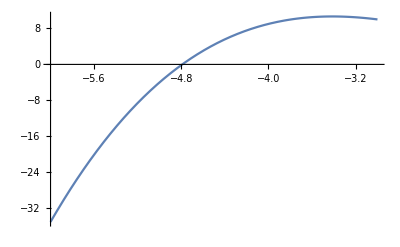

```mathematica
Plot[f[x],{x,-6,-3}]
```

```mathematica
xn2 = -0.9;
xn1 = -0.8;
xn  = -0.5;
prom = parabolINTER[xn2,xn1,xn,f];
error = Input[];
While[Abs[prom-xn]≥  error, 
xn2= xn1;
xn1 = xn;
xn = prom;
prom = parabolINTER[xn2,xn1,xn,f];
]
Print["Ответ:", N@prom ]
```

Ответ:-0.208712

```mathematica
N@Solve[x^3+6 x^2+6x+1== 0,x]
```

{{x→-1.},{x→-4.79129},{x→-0.208712}}